```mathematica
l=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.6\\python\\data.txt","Table"];
```

```mathematica
A=l[[2;;-2]];b=l[[-1]]
```

{2.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1,1,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,2.5}

```mathematica
Timing[Inverse[A].b//N]
```

{0.,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

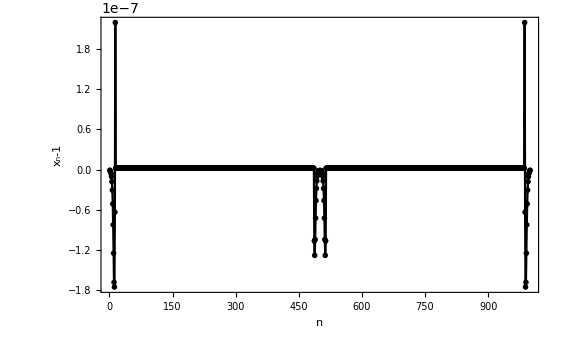

```mathematica
solution=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.6\\python\\output.txt","list"];ListPlot[solution-1,PlotTheme->"Monochrome",PlotRange->Full,Mesh->None,Joined->True,Frame->True,FrameLabel->{"n","x_n-1"},LabelStyle->{Bold, Medium}]
```

```mathematica
Norm[solution-1]
```

6.11363×10^-7